# Keeping it Sparse!

ArrayFlatten on a block matrix will be dense if any of the component blocks is dense!  The matrix for the TRS computations are 
	M0=(-B | A
A | -(g⊗g)/Δ^2) and M1=(0 | B
B | 0)
	 MM0=(Δ^2 | 0 | gᵀ
0 | -B | A
g | A | 0) and MM1=(0 | 0 | 0
0 | 0 | B
0 | B | 0)
The aim is the right most (largest positive real) eigenpair of (M0, -M1) i.e. M0.v=-λ M1.v.   If B1 is invertible the eigenvalues satisfy are the same as (M1^-1.M0).v=-λ v.  In othe words, they are the eigenvalues of MX=(M1^-1.M0)!

```mathematica
SparseArray[g]
```

SparseArray[…]

```mathematica
MM0=SparseArray[{},{2m+1,2m+1}];
MM1=SparseArray[{},{2m+1,2m+1}];
MM0⟦1,1⟧=Δ^2;
MM0⟦2;;m+1,2;;m+1⟧= -B;
MM0⟦m+2;;2m+1,2;;m+1⟧= A;
MM0⟦1,m+2;;2m+1⟧= g;
MM0⟦m+2;;2m+1,1⟧= g;
MM0⟦2;;m+1,m+2;;2m+1⟧= A;
MM1⟦m+2;;2m+1,2;;m+1⟧= B;
MM1⟦2;;m+1,m+2;;2m+1⟧= B;
Eigenvalues[{MM0, MM1}]
```

{ComplexInfinity,-6.30403+0. ⅈ,6.23434+0. ⅈ,-1.03924+0.977588 ⅈ,-1.03924-0.977588 ⅈ,0.997483+0.817445 ⅈ,0.997483-0.817445 ⅈ}

{{0.04,0,0,0,0.912235,0.207545,-0.669179},{0,-1,0,0,0.3836,1.57339,0.796631},{0,0,-1,0,1.57339,-0.423946,-0.255179},{0,0,0,-1,0.796631,-0.255179,-0.0362601},{0.912235,0.3836,1.57339,0.796631,0,0,0},{0.207545,1.57339,-0.423946,-0.255179,0,0,0},{-0.669179,0.796631,-0.255179,-0.0362601,0,0,0}}

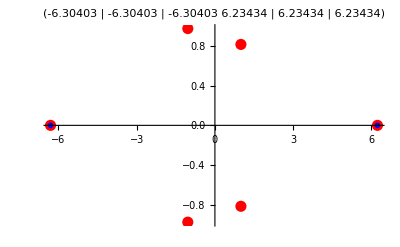

```mathematica
m=3;
A=RandomReal[{-1,1},{m,m}];A=SparseArray[A+Aᵀ];
B=SparseArray[IdentityMatrix[3]];
g=SparseArray[RandomReal[{-1,1},m]];
Δ=0.2;
M0=ArrayFlatten[({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}})];
M1=ArrayFlatten[({{0, B}, {B, 0}})];
MM0=ArrayFlatten[({{SparseArray[{{Δ^2}}], 0, {g}}, {0, -B, A}, {{g}ᵀ, A, 0}})]
MM1=ArrayFlatten[({{{{0}}, 0, 0}, {0, 0, B}, {0, B, 0}})];
MX=Inverse[M1].M0;
{AλBig,BλBig,CλBig}={
Eigenvalues[{M0,M1},2],
Eigenvalues[Inverse[M1].M0,2],
Eigenvalues[MX,2]};
Dλ=Eigenvalues[MX];
ListPlot[Map[ReIm,{Dλ,CλBig}],PlotRange->All,PlotStyle->{
Directive[Red,PointSize[0.02]],
Directive[Blue,PointSize[0.01]]},
PlotLabel->Chop[{AλBig,BλBig,CλBig}ᵀ]
]
```

```mathematica
{{λλ},{vv}}=Chop[Eigensystem[{MM0,MM1},{2}]];
{{λ},{v}}=Chop[Eigensystem[{M0,M1},{1}]];
Normalize[v⟦m+1;;2m⟧]
Normalize[vv⟦m+2;;2m+1⟧]
```

{0.53693,-0.442988,-0.71796}

{0.53693,-0.442988,-0.71796}

Doing this the naive way builds dense matrices for M0 and M1! Just fixing M1 to be sparse does not fix the issue! I need to make applying M0 efficient. Here is a function that does that

```mathematica
?LinearAlgebra`*`*
```

```mathematica
Options[LinearAlgebra`Private`Arnoldi]
```

{BasisSize→Automatic,Criteria→Automatic,MaxIterations→Automatic,Shift→Automatic,StartingVector→Automatic,Tolerance→Automatic}

```mathematica
?LinearAlgebra`LAPACK`*
```

```mathematica
Contexts[]
```

{Algebra`,Algebraics`Private`,Algebra`Polynomial`,Algebra`PolynomialPowerMod`,AlphaIntegration`,Annotation`AnnotationsDump`,Annotation`Audio`,Annotations`,Annotations`AudioDump`,Annotations`CommonDump`,Association`,Assumptions`,Astronomy`,Asymptotics`,Asymptotics`Private`,Audio`,Audio`Annotations`,Audio`AudioEffectsDump`,Audio`AudioGUIDump`,Audio`AudioMeasurementsDump`,Audio`AudioObjects`,Audio`AudioStreamDump`,Audio`AudioStreamInternals`,Audio`AudioStreamListInternals`,AudioCapture`,AudioCapture`Internals`,Audio`Developer`,Audio`EffectsDump`,AudioFileStreamTools`,Audio`Internals`,Audio`Measurements`,Audio`ResamplingOperationsDump`,Audio`SpatialOperationsDump`,Audio`SpeechDump`,Audio`StatisticOperationsDump`,Audio`Synthesis`,Audio`Utilities`,Audio`Viz`,AugmentedData`,Authentication`,BinningUtilities`,Blockchain`,BooleanAlgebra`Private`,BoxForm`,BoxFormat`,BoxForm`Private`,BrowserCategoryLoad`,Calendar`,Calendar`Legacy`,CCodeGenerator`,CCompilerDriver`,Charting`,ChatTools`,Chemistry`,Chemistry`MoleculeCaching`,CloudDialogs`,CloudExpression`Main`PackagePrivate`,CloudObject`,CloudObject`Internal`,CloudObject`Private`,CloudObject`Utilities`,CloudSystem`,CloudSystem`Private`,CloudSystem`Utility`,ClusterAnalysis`FindClusters`,Compile`,Compile`Class`,CompileDefinition`Private`,CompiledLibrary`,CompiledLibrary`EmbeddedLibrary`,Compile`Internal`,Compiler`,Compile`Utilities`,Compile`Utilities`Class`Impl`,Compile`Utilities`ClassSystem`,CompileUtilities`ClassSystem`,Compile`Utilities`Reference`Impl`,ComplexAnalysis`,ComputationalGeometry`Dump`,ComputationalGeometry`Methods`,ComputationalGeometry`Surface`,com`wolfram`jlink`ObjectMaker`,com`wolfram`jlink`Utils`,com`wolfram`textsearch`TextSearchIndex`,com`wolfram`textsearch`Tools`,Conditional`,Control`,Control`CommonDump`,Control`Conxns`,Control`Delay`,Control`DEqns`,Control`DiffGeom`,Control`Misc`,Control`NCS`,Control`Patterns`,Control`PCS`,Control`PID`,Control`PlotUtilities`,Control`PolePlace`,Control`Sim`,ControlSystems`,Control`Typesetting`,Control`Utilities`,Conversion`,Convert`TeX`,Cryptography`,Cryptography`Random`,CUDAInformation`,CURLLink`HTTP`Private`,CURLLink`Utilities`,Data`,DatabaseLink`,DatabaseLink`Information`,DataDropClient`,DataPaclets`,DataPaclets`CalendarDataDump`,DataPaclets`ColorData`,DataPaclets`Dictionary`,DataPaclets`WordConvenienceFunctionsDump`,Dataset`,DataStructure`,DateAndTime`,Debug`,Debugger`,Deconvolve`,DefinitionNotebookClient`,DemonstrationsTools`,Developer`,DeviceFramework`,Devices`Audio`,Devices`DeviceAPI`DeviceDump`,DidYouMeanIndexer`,Discrete`,Discrete`DivisorSumDump`,DiscreteMath`DecisionDiagram`,Documentation`,DocumentationSearch`,DocumentationSearcher`,DocumentationSearch`Information`,DocumentationSearch`Private`,DocumentationSearch`Skeletonizer`,DocumentationSearch`Skeletonizer`Private`,DragAndDrop`,DrawPolarAxes`,DSolve`,DynamicDump`,DynamicGeoGraphics`,ElisionsDump`,Embedded`,EntityFramework`,EntityFramework`Private`,EquationalLogic`,EquationalLogic`Private`,EquationalProof`,Experimental`,Experimental`NumericalFunction`,Explore`,Explore`ExploreDump`,ExternalEvaluate`,ExternalEvaluate`FE`,ExternalService`,ExternalService`IntegratedServices`,ExternalService`MailSettings`,ExternalService`Security`,ExternalService`URIToolsDump`,ExternalService`Utilities`,ExternalStorage`Private`,Extras`,Factor`,FE`,FE`Private`,FEPrivate`,FFmpegTools`,FFmpegTools`Audio`,FFmpegTools`Video`,FileFormatDump`,Finance`Solvers`,FindCharacterEncoding`,FindMinimum`,FindRoot`,FittedModels`,Format`,FormNotebook`,FormNotebook`Private`,FormulaData`Private`,FrontEnd`,FrontEnd`Private`,FrontEnd`WolframCloud`,FunctionProperties`,FunctionProperties`Private`,GeneralUtilities`,GenerateConditions`,GeoGraphics`,GeometricFunctions`,GeometricFunctions`BernsteinBasis`,GeometricFunctions`BSplineBasis`,GeometricFunctions`CardinalBSplineBasis`,Geometry`,Geometry`BSPTree`,Geometry`Developer`,Geometry`Mesh`,Geometry`Spatial`,GeoTools`,GIFTools`Private`,GIS`,GIS`Debug`,GraphComputation`,GraphComputation`GraphBuilderDump`,GraphComputation`GraphEditDump`,Graphics`,GraphicsArray`,Graphics`Glyphs`,Graphics`Glyphs`GlyphsDump`,GraphicsGrid`,Graphics`Legacy`,Graphics`ListParserDump`,Graphics`MapPlotDump`,Graphics`Mesh`,Graphics`Mesh`Developer`,Graphics`Mesh`FEM`,Graphics`Mesh`SoS`,Graphics`PerformanceTuningDump`,Graphics`PolygonUtils`,Graphics`PolygonUtils`Developer`,Graphics`Region`,Graphics`Region`RegionDump`,Graphics`ReliefPlotDump`,Graphics`Units`,GroebnerBasis`,GroebnerBasis`GroebnerWalk`,GroebnerGCD`,GroupTheory`PermutationGroups`,GroupTheory`PermutationGroupsDump`,GroupTheory`Symmetries`,GroupTheory`Tools`,HierarchicalClustering`,Histogram`,Holonomic`,Holonomic`Developer`,Holonomic`Private`,HTTPHandling`,HypergeometricLogDump`,Iconize`,ICULink`,ILD`,Image`,ImageAcquisition`CaptureDump`,Image`ColorOperationsDump`,Image`CompositionOperationsDump`,Image`FeaturesDump`,Image`FilteringDump`,Image`HumanDump`,Image`ImageDump`,Image`ImportExportDump`,Image`InteractiveDump`,Image`MatricesDump`,Image`MeasurementsDump`,Image`MorphologicalOperationsDump`,Image`RegistrationDump`,Image`Segmentation`,Image`SegmentationDump`,Image`SpatialOperationsDump`,ImageTransformation`,Image`TransformsDump`,Image`Utilities`,IMAPLink`,IMAQ`,IMAQ`Driver`,IMAQ`Utilities`,ImportExport`,ImportExport`Encodings`,ImportExport`FileUtilities`,ImportExport`Private`,Information`,Inpaint`,InputAssistant`,Integrate`,IntegratedServices`,Integrate`Elliptic`,Integrate`ImproperDump`,Integrate`NLtheoremDump`,InteractiveGraphics`,InteractiveGraphics`Utilities`,Internal`,Internal`MWASymbols`,Internal`ProcessEquations`,Interpreter`,Interval`,JapaneseDocumentationSearcher`,Java`,java`lang`System`,JLink`,JLink`ArgumentTests`Private`,JLink`CallJava`Private`,JLinkClassLoader`,JLink`Debug`Private`,JLink`EvaluateTo`Private`,JLink`Exceptions`Private`,JLink`FrontEndServer`Private`,JLink`Information`,JLink`InstallJava`Private`,JLink`JavaBlock`Private`,JLink`Java`Private`,JLink`JVMs`Private`,JLink`MakeJavaObject`Private`,JLink`Misc`Private`,JLink`Package`,JLink`Private`,JLink`Reflection`Private`,JLinkSandboxSecurityManager`,JLink`Sharing`Private`,JSONTools`,KeychainLink`,KeychainLink`Private`,Language`,Language`AssociationDump`,LanguageLocale`,Legending`,LibraryLink`,Limit`,LinearAlgebra`,LinearAlgebra`BLAS`,LinearAlgebra`DeconvolveDump`,LinearAlgebra`Fourier`,LinearAlgebra`LAPACK`,LinearAlgebra`LinearSolve`,LinearAlgebra`MatrixExp`,LinearAlgebra`Private`,ListableFunctionsLibrary`,LocalObjects`,LocalObjects`LocalObject`Dump`,LuceneDebug`,Macros`,Macros`ArgumentCount`PackagePrivate`,Macros`Evaluation`PackagePrivate`,Macros`Macros`PackagePrivate`,Macros`Options`PackagePrivate`,Macros`PackageScope`,MailLink`,Manipulate`,Manipulate`Dump`,MarkovProcesses`,MathLink`,MathLink`Information`,MatrixFunction`,MatrixLog`,MatrixPower`,MatrixSqrt`,MessageMenu`,Method`,MLFS`,MobileMessaging`,MultivariateResultant`,MUnit`,NaturalLanguage`,NDSolve`,NDSolve`Chasing`,NDSolve`Chasing`Implementation`,NDSolve`EventLocator`,NDSolve`FEM`,NDSolve`FEM`FEMErrorCheckingDump`,NDSolve`FEM`ShapeFunctionsDump`,NDSolve`FiniteDifferenceDerivativeFunction`,NDSolve`MethodOfLines`,NDSolve`MultistepDump`,NDSolve`Newton`,NDSolve`ProcessEquations`,NDSolve`Shooting`Implementation`,NDSolve`StateData`,NETLink`,NETLink`Information`,NETLink`Package`,Network`GraphPlot`,NeuralNetworks`,NIntegrate`,NIntegrate`OscNInt`,NMinimize`,NotebookCompatibility`,NotebookTemplating`,NotebookTemplating`Utilities`,NotebookTools`,NProduct`,NRoots`,NRoots`Private`,NSolve`,NSum`,NumberNameDump`,NumberTheory`,NumberTheory`AESDump`,NumericalFunctionCompile`,NumericalMath`,NumericalMath`NSequenceLimit`,NumericArray`,OpenCLInformation`,Optimization`,Optimization`Debug`,Optimization`FindFit`,Optimization`Fitting`,Optimization`LinearProgramming`,Optimization`LinearProgramming`Private`,Optimization`LineSearch`,Optimization`MethodFramework`,Optimization`MethodFramework`BuiltIn`,Optimization`MPSData`,Optimization`Private`,Optimization`RobustConvexOptimization`,Optimization`SolutionData`,Optimization`Transformations`,Optimization`Typeset`,Optimization`Utilities`,OutputSizeLimit`,OutputSizeLimit`Dump`,Package`,PacletManager`,PacletManager`Collection`Private`,PacletManager`Documentation`Private`,PacletManager`Extension`Private`,PacletManager`Information`,PacletManager`LayoutDocsCollection`Private`,PacletManager`Manager`Private`,PacletManager`MemoryCollection`Private`,PacletManager`Package`,PacletManager`Packer`Private`,PacletManager`Paclet`Private`,PacletManager`Private`,PacletManager`ResourceSystem`Private`,PacletManager`Services`Private`,PacletManager`Utils`Private`,PacletManager`Zip`Private`,PacletTools`,Parallel`Debug`,Parallel`Developer`,Parallel`Evaluate`,Parallel`Information`,Parallel`Palette`,Parallel`Palette`Private`,Parallel`Private`,Parallel`Settings`,Parallel`Static`,Parallel`StaticLoad`Private`,PDEModels`,PDEModels`PDEModelUtiltiesDump`,Periodic`,Periodic`Private`,Persistence`,Persistence`Data`,PersistenceLocations`,PersistenceLocations`Dump`,PlaneGeometry`,PlanetaryAstronomy`,Predictions`,PredictiveInterface`,Product`,Progress`,Progress`AssetsDump`,Progress`ProgressDump`,Proxy`,QuadraticOptimization`,Quantifier`,QuantityArray`,QuantityUnits`,QuantityUnits`Private`,QuestionFramework`,Random`,Random`Private`,RandomProcesses`,RandomProcesses`Library`,RandomProcesses`MarkovProcessUtilities`,RandomProcesses`Simulation`,RandomProcesses`TimeSeriesCommon`,RandomProcesses`Utilities`,RandomProcesses`Utilities`BuildTimeUtilitiesDump`,Random`Utilities`,Reduce`,Reduce`Private`,Region`,Region`BSPTree`,Region`Legacy`,Region`Library`,Region`Mesh`,Region`Mesh`DiscretizeGraphics`,Region`Mesh`Internal`,Region`Mesh`MarchingTables`,Region`Mesh`Utilities`,Region`Polygon`,Region`Polyhedron`,Region`Private`,Region`RegionRelationsDump`,Region`Triangulation`,RegularChains`Private`,Reliability`Library`,RemoteEvaluate`,RemoteEvaluate`Private`,RemoteKernelObject`,ResourceFunctionHelpers`,ResourceLocator`,ResourceLocator`Private`,ResourceSystemClient`,RomanNumerals`,RootReduce`Private`,RootsDump`,RSolve`,RuntimeTools`,RuntimeTools`Dump`,S3Link`,SearchResult`,SecureShellLink`,Semantic`AmbiguityDump`,Semantic`PLIDump`,Series`Private`,Services`Utilities`,Setting`,Signal`,Signal`FilterDesignDump`,Signal`FilteringDump`,Signal`FilteringIIRDump`,Signal`FiltersDump`,Signal`Resampling`,Signal`ShortTimeFourier`,Signal`ShortTimeFourierDataDump`,Signal`Utils`,SimilarityScoreMatrices`,Simplify`,Simplify`Private`,Socket`,Solve`,Sound`,Sound`SoundDump`,Sound`SoundFormatDump`,SparseArray`,SparseArray`Private`,SparseArray`SparseBlockArray`,SpatialAnalysis`,SpatialAnalysis`BirthDeathSamplers`,SpatialAnalysis`Covariance`,SpatialAnalysis`CSamplers`,SpatialAnalysis`DynamicArray`,SpatialAnalysis`Kriging`,SpatialAnalysis`Library`,SpatialAnalysis`PointDensity`,SpatialAnalysis`PointProcessFitTest`,SpatialAnalysis`RandomField`,SpatialAnalysis`SpatialPointData`Dump`,SpatialAnalysis`Temp`,SpatialAnalysis`Variogram`,SpatialPointData`,SpecialFunctions`,SpecialFunctions`Internal`,SpecialFunctions`Private`,StartUp`CriticalSection`,StartUp`Initialization`,StartUp`Initialization`InitializationValue`Dump`,StartUp`Initialization`KernelInit`Dump`,StartUp`Initialization`Static`,StartUp`LocalObjects`,StartUp`Persistence`,StartUp`Persistence`Common`Dump`,StartUp`Persistence`PersistentObject`Dump`,StartUp`Persistence`PersistentValue`Dump`,StartUp`Persistence`StandardLocations`Dump`,Statistics`,Statistics`Compatibility`,Statistics`DataDistributionUtilities`,Statistics`DerivedDistributionUtilities`,Statistics`Library`,Statistics`MCMC`,Statistics`NFunction`,Statistics`QuantityUtilities`,Statistics`RandomMatrices`,Statistics`RobustStatistics`,Statistics`SequenceOperations`,Statistics`SurvivalAnalysisTools`,Statistics`TsallisDistributionsDump`,Statistics`Utilities`,StochasticCalculus`,Stream`,Streaming`,StringPattern`,StringPattern`Dump`,StringPattern`Lexer`,StructuredArray`,StructuredArray`StructuredArrayBoxes`,StructuredArray`StructuredArrayDump`,StructuredArray`SymmetrizedArray`,StructuredArray`SymmetrizedArrayDump`,StructureDetection`,StyleManager`,SubKernels`LocalKernels`,Sum`,SurfaceGraphics`,SurfaceGraphics`Methods`,SymbolicTensors`,System`,System`BesselParamDerivativesDump`,System`CharacterFunctionsDump`,System`CompileDump`,System`ComplexDynamicsDump`,System`ComplexExpand`,System`Convert`AudioDump`,System`Convert`BitmapDump`,System`Convert`CommonArchiveDump`,System`Convert`CommonDump`,System`Convert`CommonGraphicsDump`,System`Convert`CSSDump`,System`ConvertersDump`,System`ConvertersDump`FormatUtilities`,System`ConvertersDump`Utilities`,System`ConvertersDump`Utilities`Private`,System`Convert`FlashDump`,System`Convert`HTMLDump`,System`Convert`MathMLDump`,System`Convert`NewickDump`,System`Convert`TableDump`,System`Convert`TeXDump`,System`Convert`TeXImportDump`,System`Convert`TextDump`,System`CrossDump`,System`DateObjectDump`,System`DateStringDump`,System`Dump`,System`Dump`ArgumentCount`,System`Dump`CommonPatterns`,System`Dump`DeviceAudioDump`,System`Dump`GeoLocationDump`,System`Dump`IMAQDump`,System`Dump`ParameterValidation`,System`Dump`Printout3D`,System`DynamicGeoGraphicsDump`,System`Environment`,System`FEDump`,System`FileExportListDump`,System`InfoDump`,System`InformationDump`,System`InputOutput`,System`IntegerPartitionsDump`,System`InterpolatingFunction`,System`Java`,System`LanguageEnhancements`,System`Parallel`,System`PowerReduceDump`,System`Private`,System`QuantitityUnitDefinitionDump`,System`SeriesDump`,SystemTools`,SystemTools`Private`,System`Utilities`,Tasks`,Tasks`Package`,Templating`,TemporalData`,TemporalData`Utilities`,TemporalDataUtilities`,Terminal`,TextProcessing`,TextSearch`,TextSearch`Autocomplete`PackagePrivate`,TextSearch`ContentObject`PackagePrivate`,TextSearch`Content`PackagePrivate`,TextSearch`DriverCLucene`PackagePrivate`,TextSearch`DriverLucene`PackagePrivate`,TextSearch`Driver`PackagePrivate`,TextSearch`DriverWLNative`PackagePrivate`,TextSearch`FileSearch`PackagePrivate`,TextSearch`GenerateHTTPResponse`PackagePrivate`,TextSearch`Handle`PackagePrivate`,TextSearch`Icons`PackagePrivate`,TextSearchIndex`,TextSearch`IndexCreate`PackagePrivate`,TextSearch`IndexDelete`PackagePrivate`,TextSearch`IndexSearch`PackagePrivate`,TextSearch`IndexUpdate`PackagePrivate`,TextSearch`Language`PackagePrivate`,TextSearch`LibraryLink`PackagePrivate`,TextSearch`PackageScope`,TextSearch`Private`,TextSearch`SearchIndexObject`PackagePrivate`,TextSearch`Snippet`PackagePrivate`,TextSearch`Sources`PackagePrivate`,TextSearch`TestingTools`PackagePrivate`,TextSearch`TextSearchQueryParser`PackagePrivate`,TextSearch`Tools`PackagePrivate`,TextSearch`Tools`Private`,TextSearch`Utils`PackagePrivate`,Themes`,Transforms`,TreeBrowse`,Trees`,Typeset`,Uncertainty`,URLUtilities`,URLUtilities`Build`PackagePrivate`,URLUtilities`Components`PackagePrivate`,URLUtilities`CopyFile`PackagePrivate`,URLUtilities`Encoding`PackagePrivate`,URLUtilities`Main`PackagePrivate`,URLUtilities`PackageScope`,URLUtilities`Parse`PackagePrivate`,URLUtilities`Private`,URLUtilities`Read`PackagePrivate`,URLUtilities`Shorten`PackagePrivate`,URLUtilities`Submit`PackagePrivate`,URLUtilities`Utils`PackagePrivate`,ValueTrack`,Video`,Video`EditingDump`,Video`EffectsDump`,Video`Internal`,Video`Internals`,Video`Iterator`,VideoStream`,Video`TranscodeDump`,Video`Utilities`,Video`VideoJoinDump`,Video`VideoStreamDump`,Video`VideoStreamInternals`,Video`VideoUtilitiesGlobalDump`,Visualization`,Visualization`Core`,Visualization`Interpolation`,Visualization`LegendsDump`,Visualization`Utilities`,Visualization`VectorFields`,Visualization`VectorFields`VectorFieldsDump`,Wavelets`,Wavelets`LiftingFilter`,Wavelets`WaveletData`,Wavelets`WaveletListPlot`,Wavelets`WaveletPlot2D`,Wavelets`WaveletScalogram`,Wavelets`WaveletUtilities`,WebServices`,WebServices`Information`,WolframAppCatalog`,WolframAppCatalog`Private`,WolframCGL`,WSTP`LinkServer`,WSTP`ServiceDiscovery`,XML`,XML`MathML`,XML`MathML`Symbols`,XML`NotebookML`,XML`Parser`,XML`RSS`,XML`SVG`}

```mathematica
Names["`*`Ar*`*"]
```

{}

```mathematica
M0Fun[A_,B_,g_,Δ_,m_][x_]:= Module[{p1,p2},
{p1,p2}=Partition[x,m];
Join[-B.p1+A.p2,A.p1 -g(g.p2)/Δ^2]
]
```

```mathematica
m=3;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
B=IdentityMatrix[3];
g=RandomReal[{-1,1},m];
Δ=0.2;
M0=ArrayFlatten[({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}})];
Norm[M0Fun[A,B,g,Δ,m][v]-M0.v]
```

1.01791×10^-15

The question here is how can we use this in an eigenvalue routine.

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}];
v0=Normalize[RandomReal[{-1,1},m]];
Afun[v_]:=A.v
Eigenvalues[A,3,Method->{"Arnoldi","BasisSize"->5,"StartingVector"->v0}]
```

{-1.80407+1.46581 ⅈ,-1.80407-1.46581 ⅈ,-0.593212+1.55491 ⅈ}